# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisPtb1.txt"}]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
(*tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]*)

SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/PentaBoxImportingPureInts/KIRA/splitres/phasespace_00001.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];



PureIntegralN=Expand[PureIntegrals/.tPoint/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
epsrepl={(ep->(4-d)/2)/.tPoint};
```

{d→1601280545,mt2→720068054,s12→1983291274,s123→274979641,s16→412362128,s23→491616724,s234→1894747477,s34→713649962,s345→2097893744,s45→994203284,s56→1659670790}

2.13411

# Compute Basis Change Matrix

74

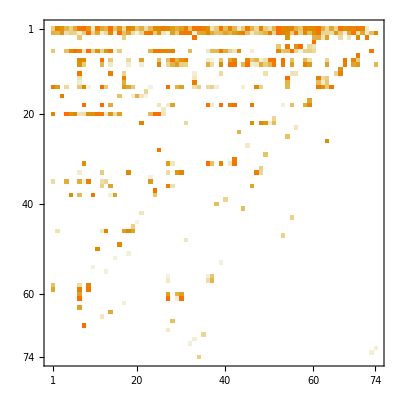

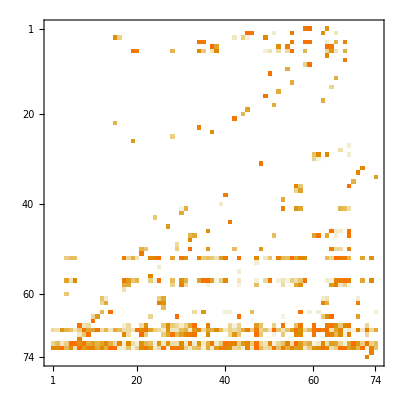

```mathematica
(*reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];*)
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,74}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
BasisChangMatInv//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[Delete[{1,2,3,4,5,6,7,8,9,10,11},var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*74+intpos,{1,74*10}],"  ",var,"/10 ",intpos,"/74"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

6452

```mathematica
ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

545

```mathematica
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

```mathematica
WriteJobFile[{"ExtraRelationsReduList","UReduList","ReduList"}]
```

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
```

6452

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

332

# Compute DE Matrices

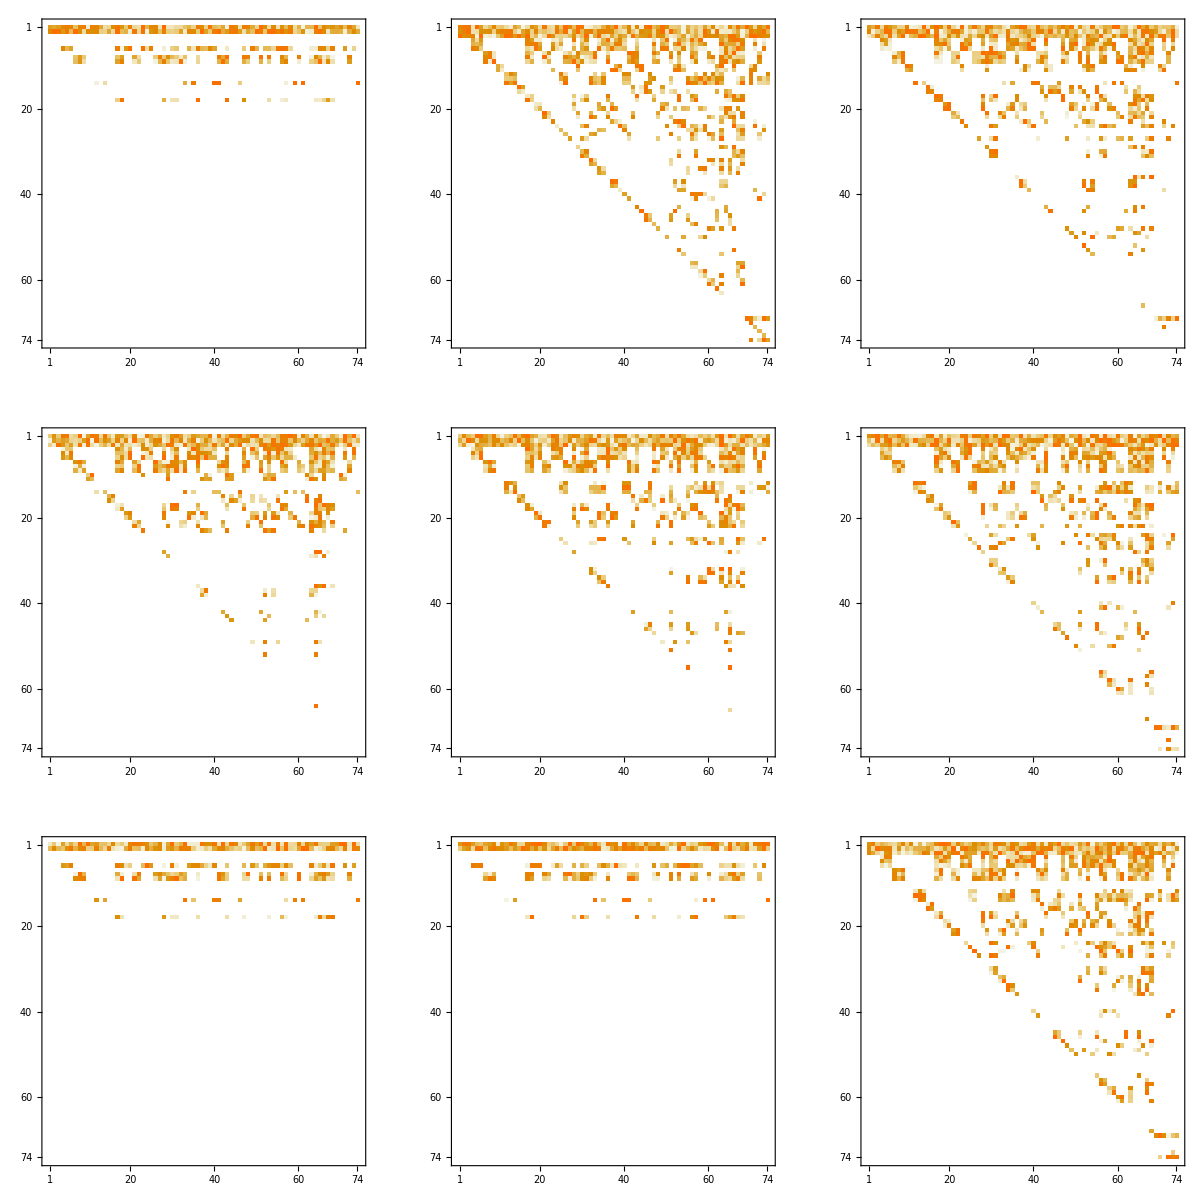

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,74]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3},{Mplot4,Mplot5,Mplot6},{Mplot7,Mplot8,Mplot9}}]
```

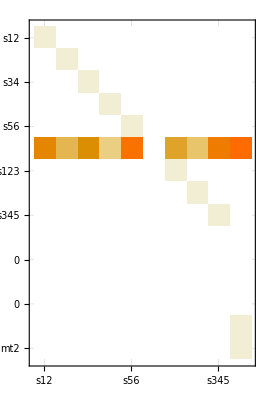

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

```mathematica
checkDifferentialOperator[tPoint,diffOp]
```

```mathematica
tPoint//Length
```

11

```mathematica
invariantsnodUpperCase
```

invariantsnodUpperCase

```mathematica
diffInts[[10,74]]
```

140909335 hxb[0,0,2,0,1,0,1,0,1,0,0,0,0]+1551520144 hxb[1,-1,2,0,1,0,1,0,1,0,0,0,0]+795937619 hxb[1,0,1,0,0,0,2,0,1,0,0,0,0]+958699721 hxb[1,0,1,0,1,-1,2,0,1,0,0,0,0]+329225148 hxb[1,0,1,0,1,0,1,0,1,0,0,0,0]+1025742892 hxb[1,0,1,0,1,0,2,0,0,0,0,0,0]+1551520144 hxb[1,0,1,0,1,0,2,0,1,0,0,0,-1]+2067126627 hxb[1,0,1,0,1,0,2,0,1,0,0,0,0]+958699721 hxb[1,0,1,0,2,-1,1,0,1,0,0,0,0]+2110550565 hxb[1,0,1,0,2,0,0,0,1,0,0,0,0]+1025742892 hxb[1,0,1,0,2,0,1,0,0,0,0,0,0]+1551520144 hxb[1,0,1,0,2,0,1,0,1,0,0,0,-1]+1982575814 hxb[1,0,1,0,2,0,1,0,1,0,0,0,0]+921766639 hxb[1,0,2,0,1,0,1,0,1,-1,0,0,0]+2110550565 hxb[1,0,2,0,1,0,1,0,1,0,-1,0,0]+688429614 hxb[1,0,2,0,1,0,1,0,1,0,0,0,0]+95997863 hxb[1,0,1,0,1,0,2,0,1,0,0,0,0] p[1]^2+95997863 hxb[1,0,1,0,2,0,1,0,1,0,0,0,0] p[1]^2+95997863 hxb[1,0,2,0,1,0,1,0,1,0,0,0,0] p[1]^2+1287924869 hxb[1,0,1,0,1,0,2,0,1,0,0,0,0] p[2]^2+1287924869 hxb[1,0,1,0,2,0,1,0,1,0,0,0,0] p[2]^2+1287924869 hxb[1,0,2,0,1,0,1,0,1,0,0,0,0] p[2]^2+1843533278 hxb[1,0,1,0,1,0,2,0,1,0,0,0,0] p[3]^2+2073617483 hxb[1,0,1,0,1,0,2,0,1,0,0,0,0] p[4]^2

```mathematica
Monitor[Table[Length[FactorInteger[2^n-1]],{n,50,500,50}],Row[{ProgressIndicator[n,{1,500}],n}]]
```

{7,12,13,18,11,25,20,24,24,22}

```mathematica
Cases[PureIntegralN2,_hxb,Infinity]//DeleteDuplicates
```

{hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0]}

241

```mathematica
SubLaporta=Cases[PureIntegralN2,_hxb,Infinity]//DeleteDuplicates;
```

```mathematica
PureIntegralN2[[5]]
```

1213129225 ep^4 hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0]+1785818152 ep^4 hxb[1,1,1,1,0,0,1,0,1,0,0,0,0]+1230783587 ep^4 hxb[1,1,1,1,0,1,0,0,1,0,0,0,0]+1715891795 ep^4 hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0]+1814294158 ep^4 hxb[1,1,1,1,0,1,1,0,0,0,0,0,0]+799273033 ep^4 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]

```mathematica
PureIntegralN2
```

```mathematica
PureIntegralN2[[12]]
PureIntegrals[[12]]
```

0

ep^4 s12^2 s234 hxb[1,1,1,1,1,0,1,0,1,0,0,0,0]

```mathematica
NullInts
```

{hxb[0,0,1,1,1,1,0,0,0,0,0,0,0]→0,hxb[0,1,1,0,0,1,1,0,1,0,0,0,0]→0,hxb[0,1,1,0,1,0,1,0,1,0,0,0,0]→0,hxb[0,1,1,0,1,1,0,0,1,0,0,0,0]→0,hxb[0,1,1,0,1,1,1,0,0,0,0,0,0]→0,hxb[0,1,1,0,1,1,1,0,1,0,0,0,-1]→0,hxb[0,1,1,0,1,1,1,0,1,0,0,0,0]→0,hxb[1,1,0,0,0,1,1,0,1,0,0,0,0]→0,hxb[1,1,0,0,1,0,1,0,1,0,0,0,0]→0,hxb[1,1,0,0,1,1,0,0,1,0,0,0,0]→0,hxb[1,1,0,0,1,1,1,0,0,0,0,0,0]→0,hxb[1,1,0,0,1,1,1,0,1,0,0,0,-1]→0,hxb[1,1,0,0,1,1,1,0,1,0,0,0,0]→0,hxb[1,1,1,1,1,0,1,0,1,0,0,0,0]→0,hxb[1,1,1,1,1,1,0,-1,1,0,0,0,0]→0}

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
```

```mathematica
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];
```

```mathematica
Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//Length
Cases[PureIntegralN3,_hxb,Infinity]//DeleteDuplicates//Length
Cases[PureIntegralN2,_hxb,Infinity]//DeleteDuplicates//Length
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
```

545

87

89

```mathematica
NonZeros//Length
Ureduce//Length
ZeroInts=Complement[Ureduce,NonZeros]
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;
```

6602

545

{hxb[0,0,1,1,1,1,0,0,0,0,0,0,0],hxb[0,1,1,0,0,1,1,0,1,0,0,0,0],hxb[0,1,1,0,1,0,1,0,1,0,0,0,0],hxb[0,1,1,0,1,1,0,0,1,0,0,0,0],hxb[0,1,1,0,1,1,1,0,0,0,0,0,0],hxb[0,1,1,0,1,1,1,0,1,0,0,0,-1],hxb[0,1,1,0,1,1,1,0,1,0,0,0,0],hxb[1,1,0,0,0,1,1,0,1,0,0,0,0],hxb[1,1,0,0,1,0,1,0,1,0,0,0,0],hxb[1,1,0,0,1,1,0,0,1,0,0,0,0],hxb[1,1,0,0,1,1,1,0,0,0,0,0,0],hxb[1,1,0,0,1,1,1,0,1,0,0,0,-1],hxb[1,1,0,0,1,1,1,0,1,0,0,0,0]}

74

```mathematica
PureIntegralN4//Length
```

74

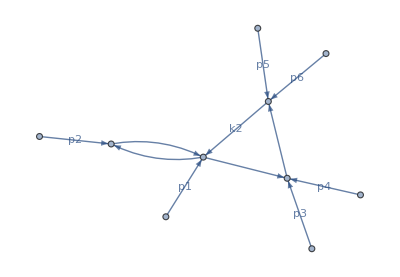

```mathematica
plotDiagram[ZeroInts[[3]]]
```

```mathematica
invariants
```

{d,mt2,s12,s123,s16,s23,s234,s34,s345,s45,s56}

```mathematica
SubLaporta
```

{hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0]}

```mathematica
PureIntegralN[[3]]
PureIntegralN2[[3]]
PureIntegralN3[[3]]
PureIntegralN4[[3]]
```

447777870 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]

1546288730 ep^4 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+1861841858 ep^4 hxb[1,1,1,1,1,0,1,0,1,0,0,0,0]+843136098 ep^4 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+610107277 ep^4 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+2028854848 ep^4 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1892433609 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

1106489225 ep^4 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]+381387392 ep^4 hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]+2010436643 ep^4 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]+407170895 ep^4 hxb[1,1,1,1,0,0,1,0,1,0,0,0,0]+1546288730 ep^4 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+202912829 ep^4 hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0]+399321981 ep^4 hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0]+378717531 ep^4 hxb[1,1,1,1,1,0,1,0,0,0,0,0,0]+843136098 ep^4 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+610107277 ep^4 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+2028854848 ep^4 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1892433609 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

723621755 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]+633921554 hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]+2041566529 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]+1340492732 hxb[1,1,1,1,0,0,1,0,1,0,0,0,0]+1012667526 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+1036031177 hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0]+273706585 hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0]+1143329231 hxb[1,1,1,1,1,0,1,0,0,0,0,0,0]+412221300 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+234743020 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+1408028418 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1783410273 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

```mathematica
SetA=Cases[Expand[PureIntegralN2/.ZeroIntsRepl/.epsrepl,Modulus->$P],_hxb,Infinity]//DeleteDuplicates;
```

```mathematica
SetB=Cases[Expand[PureIntegralN4,Modulus->$P],_hxb,Infinity]//DeleteDuplicates;
```

```mathematica
Complement[SetA,SetB]
Complement[SetB,SetA]
```

{hxb[1,1,1,1,1,0,1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,-1,1,0,0,0,0]}

{}

```mathematica
SetB
```

{hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0]}

```mathematica
PtbMasters=Cases[ReadList[FileNameJoin[{NotebookDirectory[],"mastersPTB"}]],_ptb,Infinity];
PtbMasters=PtbMasters/.ptb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_]:>hxb[n1,n2,n3,n4,n5,n6,n7,0,n8,0,n9,n10,n11]
```

{hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,0,-1,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,-1,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]}

```mathematica
CSET=Complement[SetB,PtbMasters]
CSET2=Complement[PtbMasters,SetB]
```

{hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,1,-1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,-1,0,0,0]}

{hxb[1,1,1,1,0,1,1,0,1,0,-1,0,0],hxb[1,1,1,1,1,0,1,0,1,0,-1,0,0],hxb[1,1,1,1,1,0,1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]}

```mathematica
Position[PureIntegralN4,CSET[[1]]]
Position[PureIntegralN4,CSET[[2]]]
Position[PureIntegralN4,CSET[[3]]]
Position[PureIntegralN4,CSET[[4]]]
Position[PureIntegralN4,CSET[[5]]]
Position[PureIntegralN4,CSET[[6]]]

Position[PureIntegralN,CSET2[[6]]]
```

{{1,57,2},{2,59,2},{5,4,2},{6,37,2}}

{{1,62,2},{2,64,2},{3,7,2},{12,6,2},{13,6,2},{14,26,2}}

{{1,64,2},{2,66,2},{14,28,2}}

{{1,67,2},{2,69,2},{8,30,2},{9,32,2}}

{{1,68,2},{2,70,2},{3,10,2}}

{{1,71,2},{2,73,2}}

{{1,36,3},{2,2,887,3},{2,2,888,3},{3,3}}

```mathematica
Complement[LaportaBasis,SubLaporta]
Complement[SubLaporta,LaportaBasis]
```

{hxb[-1,0,1,1,0,0,0,1,0,0,0,0,0],hxb[-1,0,1,1,0,0,1,1,1,0,0,0,0],hxb[-1,0,1,1,0,1,0,1,1,0,0,0,0],hxb[-1,0,1,1,0,1,1,1,1,0,0,0,0],hxb[-1,1,0,1,0,0,0,1,0,0,0,0,0],hxb[-1,1,0,1,0,0,1,1,1,0,0,0,0],hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0],hxb[-1,1,0,1,0,1,0,1,1,0,0,0,0],hxb[-1,1,0,1,0,1,1,1,1,0,0,0,0],hxb[-1,1,0,1,1,0,0,1,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,1,0,0,0,0,0],hxb[-1,1,0,1,1,0,1,1,1,0,0,0,0],hxb[-1,1,0,1,1,1,0,1,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,1,0,0,0,0,0],hxb[-1,1,0,1,1,1,1,1,1,0,0,0,0],hxb[-1,1,1,1,0,0,0,1,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,1,0,0,0,0,0],hxb[-1,1,1,1,0,0,1,1,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,1,0,0,0,0,0],hxb[-1,1,1,1,0,1,0,1,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,1,0,0,0,0,0],hxb[-1,1,1,1,0,1,1,1,1,0,0,0,0],hxb[0,0,1,1,0,0,0,1,0,0,0,0,0],hxb[0,0,1,1,0,0,0,1,1,0,0,0,0],hxb[0,0,1,1,0,0,1,1,0,0,0,0,0],hxb[0,0,1,1,0,0,1,1,1,0,0,0,0],hxb[0,0,1,1,0,1,0,1,0,0,0,0,0],hxb[0,0,1,1,0,1,0,1,1,0,0,0,0],hxb[0,0,1,1,0,1,1,1,0,0,0,0,0],hxb[0,0,1,1,0,1,1,1,1,0,0,0,0],hxb[0,1,0,1,0,0,0,1,0,0,0,0,0],hxb[0,1,0,1,0,0,1,1,0,0,0,0,0],hxb[0,1,0,1,0,0,1,1,1,0,0,0,0],hxb[0,1,0,1,0,1,0,1,0,0,0,0,0],hxb[0,1,0,1,0,1,0,1,1,0,0,0,0],hxb[0,1,0,1,0,1,1,1,0,0,0,0,0],hxb[0,1,0,1,0,1,1,1,1,0,0,0,0],hxb[0,1,0,1,1,0,0,1,0,0,0,0,0],hxb[0,1,0,1,1,0,0,1,1,0,0,0,0],hxb[0,1,0,1,1,0,1,1,0,0,0,0,0],hxb[0,1,0,1,1,0,1,1,1,0,0,0,0],hxb[0,1,0,1,1,1,0,1,0,0,0,0,0],hxb[0,1,0,1,1,1,0,1,1,0,0,0,0],hxb[0,1,0,1,1,1,1,1,0,0,0,0,0],hxb[0,1,1,1,0,0,0,1,1,0,0,0,0],hxb[0,1,1,1,0,0,1,1,0,0,0,0,0],hxb[0,1,1,1,0,0,1,1,1,0,0,0,0],hxb[0,1,1,1,0,1,0,1,0,0,0,0,0],hxb[0,1,1,1,0,1,0,1,1,0,0,0,0],hxb[0,1,1,1,0,1,1,1,0,0,0,0,0],hxb[1,-1,1,1,0,0,0,1,0,0,0,0,0],hxb[1,-1,1,1,0,0,1,1,0,0,0,0,0],hxb[1,-1,1,1,0,1,0,1,0,0,0,0,0],hxb[1,-1,1,1,0,1,1,1,0,0,0,0,0],hxb[1,0,0,1,0,0,0,1,0,0,0,0,0],hxb[1,0,0,1,0,0,1,1,0,0,0,0,0],hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0],hxb[1,0,0,1,0,1,0,1,0,0,0,0,0],hxb[1,0,0,1,0,1,1,1,0,0,0,0,0],hxb[1,0,0,1,1,0,0,1,-1,0,0,0,0],hxb[1,0,0,1,1,0,0,1,0,0,0,0,0],hxb[1,0,0,1,1,0,1,1,-1,0,0,0,0],hxb[1,0,0,1,1,0,1,1,0,0,0,0,0],hxb[1,0,0,1,1,1,0,1,0,0,0,0,0],hxb[1,0,0,1,1,1,1,1,-1,0,0,0,0],hxb[1,0,0,1,1,1,1,1,0,0,0,0,0],hxb[1,0,1,0,0,0,0,1,0,0,0,0,0],hxb[1,0,1,0,0,0,1,1,1,0,0,0,0],hxb[1,0,1,0,0,1,0,1,0,0,0,0,0],hxb[1,0,1,0,0,1,0,1,1,0,0,0,0],hxb[1,0,1,0,0,1,1,1,1,0,0,0,0],hxb[1,0,1,0,1,0,0,1,0,0,0,0,0],hxb[1,0,1,0,1,0,0,1,1,0,0,0,0],hxb[1,0,1,0,1,0,1,1,0,0,0,0,0],hxb[1,0,1,0,1,0,1,1,1,0,0,0,0],hxb[1,0,1,0,1,1,0,1,1,0,0,0,0],hxb[1,0,1,0,1,1,1,1,0,0,0,0,0],hxb[1,0,1,0,1,1,1,1,1,0,0,0,0],hxb[1,0,1,1,-1,0,1,1,0,0,0,0,0],hxb[1,0,1,1,-1,1,0,1,0,0,0,0,0],hxb[1,0,1,1,-1,1,1,1,0,0,0,0,0],hxb[1,0,1,1,0,0,0,1,-1,0,0,0,0],hxb[1,0,1,1,0,0,0,1,0,0,0,0,0],hxb[1,0,1,1,0,0,1,1,-2,0,0,0,0],hxb[1,0,1,1,0,0,1,1,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,1,0,-1,0,0,0],hxb[1,0,1,1,0,0,1,1,0,0,0,0,0],hxb[1,0,1,1,0,0,1,1,1,0,0,0,0],hxb[1,0,1,1,0,1,0,1,-2,0,0,0,0],hxb[1,0,1,1,0,1,0,1,-1,0,0,0,0],hxb[1,0,1,1,0,1,0,1,0,-1,0,0,0],hxb[1,0,1,1,0,1,0,1,0,0,0,0,0],hxb[1,0,1,1,0,1,0,1,1,0,0,0,0],hxb[1,0,1,1,0,1,1,1,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,1,0,-1,0,0,0],hxb[1,0,1,1,0,1,1,1,0,0,-1,0,0],hxb[1,0,1,1,0,1,1,1,0,0,0,0,0],hxb[1,0,1,1,0,1,1,1,1,0,0,0,0],hxb[1,0,1,1,1,0,0,1,0,0,0,0,0],hxb[1,0,1,1,1,0,1,1,0,0,0,0,0],hxb[1,0,1,1,1,1,0,1,0,0,0,0,0],hxb[1,0,1,1,1,1,1,1,0,0,0,0,0],hxb[1,1,0,1,0,0,1,1,-1,0,0,0,0],hxb[1,1,0,1,0,0,1,1,0,0,0,0,0],hxb[1,1,0,1,0,1,0,1,-1,0,0,0,0],hxb[1,1,0,1,0,1,0,1,0,0,0,0,0],hxb[1,1,0,1,0,1,1,1,-1,0,0,0,0],hxb[1,1,0,1,0,1,1,1,0,0,0,0,0],hxb[1,1,0,1,1,0,0,1,-1,0,0,0,0],hxb[1,1,0,1,1,0,0,1,0,0,0,0,0],hxb[1,1,0,1,1,0,1,1,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,1,0,0,0,0,0],hxb[1,1,0,1,1,1,0,1,-1,0,0,0,0],hxb[1,1,0,1,1,1,0,1,0,0,0,0,0],hxb[1,1,0,1,1,1,1,1,0,0,0,0,0],hxb[1,1,1,1,-1,0,1,1,0,0,0,0,0],hxb[1,1,1,1,-1,0,1,1,1,0,0,0,0],hxb[1,1,1,1,-1,1,0,1,0,0,0,0,0],hxb[1,1,1,1,-1,1,0,1,1,0,0,0,0],hxb[1,1,1,1,-1,1,1,1,-1,0,0,0,0],hxb[1,1,1,1,-1,1,1,1,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,1,1,0,0,0,0],hxb[1,1,1,1,0,-1,1,1,0,0,0,0,0],hxb[1,1,1,1,0,-1,1,1,1,0,0,0,0],hxb[1,1,1,1,0,0,0,1,-1,0,0,0,0],hxb[1,1,1,1,0,0,0,1,0,0,0,0,0],hxb[1,1,1,1,0,0,1,1,-1,0,0,0,0],hxb[1,1,1,1,0,0,1,1,0,-1,0,0,0],hxb[1,1,1,1,0,0,1,1,0,0,0,0,0],hxb[1,1,1,1,0,0,1,1,1,-1,0,0,0],hxb[1,1,1,1,0,0,1,1,1,0,0,0,0],hxb[1,1,1,1,0,1,-1,1,0,0,0,0,0],hxb[1,1,1,1,0,1,-1,1,1,0,0,0,0],hxb[1,1,1,1,0,1,0,1,-1,0,0,0,0],hxb[1,1,1,1,0,1,0,1,0,-1,0,0,0],hxb[1,1,1,1,0,1,0,1,0,0,-1,0,0],hxb[1,1,1,1,0,1,0,1,0,0,0,0,0],hxb[1,1,1,1,0,1,0,1,1,-1,0,0,0],hxb[1,1,1,1,0,1,0,1,1,0,0,0,0],hxb[1,1,1,1,0,1,1,1,-2,0,0,0,0],hxb[1,1,1,1,0,1,1,1,-1,-1,0,0,0],hxb[1,1,1,1,0,1,1,1,0,-1,0,0,0],hxb[1,1,1,1,0,1,1,1,0,0,-1,0,0],hxb[1,1,1,1,0,1,1,1,0,0,0,0,0],hxb[1,1,1,1,0,1,1,1,1,-1,0,0,0],hxb[1,1,1,1,0,1,1,1,1,0,-1,0,0],hxb[1,1,1,1,1,-1,0,1,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,1,0,0,0,0,0],hxb[1,1,1,1,1,-1,1,1,1,0,0,0,0],hxb[1,1,1,1,1,0,-1,1,1,0,0,0,0],hxb[1,1,1,1,1,0,0,1,0,0,0,0,0],hxb[1,1,1,1,1,0,0,1,1,-1,0,0,0],hxb[1,1,1,1,1,0,1,1,-1,0,0,0,0],hxb[1,1,1,1,1,0,1,1,0,-1,0,0,0],hxb[1,1,1,1,1,0,1,1,0,0,0,0,0],hxb[1,1,1,1,1,0,1,1,1,-1,0,0,0],hxb[1,1,1,1,1,0,1,1,1,0,0,0,0],hxb[1,1,1,1,1,1,-1,1,0,0,0,0,0],hxb[1,1,1,1,1,1,-1,1,1,0,0,0,0],hxb[1,1,1,1,1,1,0,1,-1,0,0,0,0],hxb[1,1,1,1,1,1,0,1,0,0,0,0,0],hxb[1,1,1,1,1,1,0,1,1,-1,0,0,0],hxb[1,1,1,1,1,1,0,1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,1,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,1,0,-1,0,0,0],hxb[1,1,1,1,1,1,1,1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,1,1,0,0,0,0]}

{}

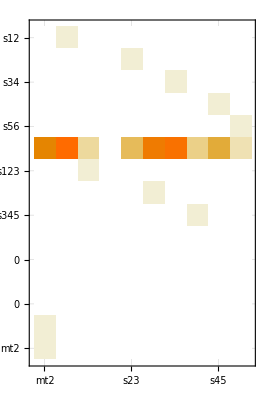

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

del[s12]+2084416764 del[s16]+1712988205 del[p[1]] p[1]+2061251010 del[p[5]] p[1]+520728079 del[p[6]] p[1]+925125639 del[p[1]] p[2]+1033356342 del[p[5]] p[2]+189001666 del[p[6]] p[2]+1688805657 del[p[1]] p[3]+746509143 del[p[5]] p[3]+1859652494 del[p[6]] p[3]+1648183300 del[p[1]] p[4]+1674389614 del[p[5]] p[4]+972394380 del[p[6]] p[4]

```mathematica
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
checkDifferentialOperator[tPoint,diffOp]
```

```mathematica
Expand[(applyDifferentialOperator[Coefficient[diffOp,ds[S12]],(p[6])^2]/.p4conv//Expand)/.mandelstamScalarProducts/.tPoint,Modulus->$P]
```

0

```mathematica
invariantsnod
```

{mt2,s12,s123,s16,s23,s234,s34,s345,s45,s56}

```mathematica
PureIntegrals[[3]]
PureIntegralN[[3]]
PureIntegralN2[[3]]
PureIntegralN3[[3]]
PureIntegralN4[[3]]
```

ep^4 s12 s123 s34 hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]

447777870 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]

1546288730 ep^4 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+1861841858 ep^4 hxb[1,1,1,1,1,0,1,0,1,0,0,0,0]+843136098 ep^4 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+610107277 ep^4 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+2028854848 ep^4 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1892433609 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

1106489225 ep^4 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]+381387392 ep^4 hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]+2010436643 ep^4 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]+407170895 ep^4 hxb[1,1,1,1,0,0,1,0,1,0,0,0,0]+1546288730 ep^4 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+202912829 ep^4 hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0]+399321981 ep^4 hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0]+378717531 ep^4 hxb[1,1,1,1,1,0,1,0,0,0,0,0,0]+843136098 ep^4 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+610107277 ep^4 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+2028854848 ep^4 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1892433609 ep^4 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

723621755 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]+633921554 hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]+2041566529 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]+1340492732 hxb[1,1,1,1,0,0,1,0,1,0,0,0,0]+1012667526 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+1036031177 hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0]+273706585 hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0]+1143329231 hxb[1,1,1,1,1,0,1,0,0,0,0,0,0]+412221300 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+234743020 hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0]+1408028418 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1783410273 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]

```mathematica
PtbMasters
```

{hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,0,-1,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,-1,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,-1,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]}

```mathematica
diffInts[[2,3]]
PureIntegrals[[3]]
```

1185845506 hxb[0,1,2,1,1,1,1,0,1,0,0,0,-1]+1185845506 hxb[0,2,1,1,1,1,1,0,1,0,0,0,-1]+1403243020 hxb[1,0,2,1,1,1,1,0,1,0,0,0,-1]+1960584766 hxb[1,1,1,1,0,1,1,0,1,0,0,0,0]+186898881 hxb[1,1,1,1,0,1,2,0,1,0,0,0,-1]+186898881 hxb[1,1,1,1,0,2,1,0,1,0,0,0,-1]+555225598 hxb[1,1,1,1,1,0,1,0,1,0,0,0,0]+1592258049 hxb[1,1,1,1,1,0,2,0,1,0,0,0,-1]+555178737 hxb[1,1,1,1,1,1,0,0,1,0,0,0,0]+479737566 hxb[1,1,1,1,1,1,1,0,0,0,0,0,0]+1220719445 hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]+848118492 hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]+1667746081 hxb[1,1,1,1,1,1,2,0,0,0,0,0,-1]+1403243020 hxb[1,1,1,1,1,1,2,0,1,0,0,0,-2]+1299365155 hxb[1,1,1,1,1,1,2,0,1,0,0,0,-1]+1592304910 hxb[1,1,1,1,1,2,0,0,1,0,0,0,-1]+1667746081 hxb[1,1,1,1,1,2,1,0,0,0,0,0,-1]+1403243020 hxb[1,1,1,1,1,2,1,0,1,0,0,0,-2]+1299365155 hxb[1,1,1,1,1,2,1,0,1,0,0,0,-1]+1592258049 hxb[1,1,1,1,2,0,1,0,1,0,0,0,-1]+1592304910 hxb[1,1,1,1,2,1,0,0,1,0,0,0,-1]+1667746081 hxb[1,1,1,1,2,1,1,0,0,0,0,0,-1]+1403243020 hxb[1,1,1,1,2,1,1,0,1,0,0,0,-2]+1134139449 hxb[1,1,1,1,2,1,1,0,1,0,0,0,-1]+1037079312 hxb[1,1,2,1,1,1,1,0,1,-1,0,0,-1]+1592304910 hxb[1,1,2,1,1,1,1,0,1,0,-1,0,-1]+1163390222 hxb[1,1,2,1,1,1,1,0,1,0,0,0,-1]+1223978193 hxb[1,2,0,1,1,1,1,0,1,0,0,0,-1]+1037079312 hxb[1,2,1,1,1,1,1,0,1,-1,0,0,-1]+1592304910 hxb[1,2,1,1,1,1,1,0,1,0,-1,0,-1]+1328615928 hxb[1,2,1,1,1,1,1,0,1,0,0,0,-1]

ep^4 s12 s123 s34 hxb[1,1,1,1,1,1,1,0,1,0,0,0,-1]

```mathematica
diffs12A3=Expand[diffInts[[2,2]]/.ReductionRules,Modulus->$P];
SETA=Cases[diffs12A3,_hxb,Infinity]//DeleteDuplicates;
diffs12B3=Expand[diffs12A3/.ExtraRelations,Modulus->$P];
SETB=Cases[diffs12B3,_hxb,Infinity]//DeleteDuplicates;

nulllist=Thread[Rule[Complement[SETB,SubLaporta],0]];

diffs12A3=Expand[diffInts[[2,2]]/.ReductionRules/.nulllist,Modulus->$P];
SETA=Cases[diffs12A3,_hxb,Infinity]//DeleteDuplicates;
diffs12B3=Expand[diffs12A3/.ExtraRelations,Modulus->$P];
SETB=Cases[diffs12B3,_hxb,Infinity]//DeleteDuplicates;

Complement[SETA,SETB]
Complement[SETB,SETA]
SETA//Length
SETB//Length
```

{hxb[1,1,1,1,1,0,1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,-1,1,0,0,0,0]}

{}

76

74

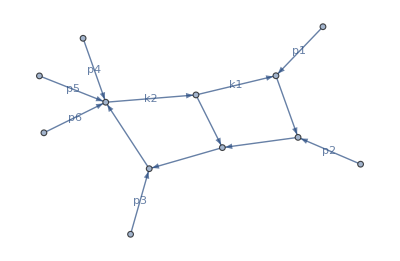

```mathematica
plotDiagram[hxb[1,1,1,1,1,1,0,-1,1,0,0,0,0]]
```

{hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,0,1,0,1,0,0,0,0],hxb[-1,1,0,1,1,1,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[-1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[0,0,1,1,0,0,0,0,1,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[0,0,1,1,0,0,1,0,1,0,0,0,0],hxb[0,0,1,1,0,1,0,0,1,0,0,0,0],hxb[0,0,1,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,0,0,1,0,0,0,0,0,0],hxb[0,1,0,1,0,0,1,0,1,0,0,0,0],hxb[0,1,0,1,0,1,0,0,0,0,0,0,0],hxb[0,1,0,1,0,1,0,0,1,0,0,0,0],hxb[0,1,0,1,0,1,1,0,1,0,0,0,0],hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],hxb[0,1,0,1,1,0,1,0,0,0,0,0,0],hxb[0,1,0,1,1,0,1,0,1,0,0,0,0],hxb[0,1,0,1,1,1,0,0,1,0,0,0,0],hxb[0,1,0,1,1,1,1,0,0,0,0,0,0],hxb[0,1,0,1,1,1,1,0,1,0,0,0,0],hxb[0,1,1,1,0,0,1,0,1,0,0,0,0],hxb[0,1,1,1,0,1,0,0,1,0,0,0,0],hxb[0,1,1,1,0,1,1,0,0,0,0,0,0],hxb[0,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[1,0,0,1,0,1,0,0,0,0,0,0,0],hxb[1,0,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,0,0,1,1,0,1,0,0,0,0,0,0],hxb[1,0,0,1,1,1,1,0,0,0,0,0,0],hxb[1,0,1,0,0,0,1,0,1,0,0,0,0],hxb[1,0,1,0,0,1,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],hxb[1,0,1,0,1,0,1,0,0,0,0,0,0],hxb[1,0,1,0,1,0,1,0,1,0,0,0,0],hxb[1,0,1,0,1,1,1,0,1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,1,0,0,0,0],hxb[1,0,1,1,0,1,0,0,0,0,0,0,0],hxb[1,0,1,1,0,1,0,0,1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,1,1,0,0,0,0,0,0],hxb[1,0,1,1,0,1,1,0,1,0,0,0,0],hxb[1,0,1,1,1,0,1,0,0,0,0,0,0],hxb[1,0,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,0,1,0,1,1,0,0,0,0,0,0],hxb[1,1,0,1,1,0,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,0,1,0,0,0,0,0,0],hxb[1,1,0,1,1,1,0,0,0,0,0,0,0],hxb[1,1,0,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,0,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,-1,1,1,0,1,0,0,0,0],hxb[1,1,1,1,0,0,1,0,0,0,0,0,0],hxb[1,1,1,1,0,0,1,0,1,0,0,0,0],hxb[1,1,1,1,0,1,0,0,0,0,0,0,0],hxb[1,1,1,1,0,1,0,0,1,0,0,0,0],hxb[1,1,1,1,0,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,0,1,1,0,0,0,0,0,0],hxb[1,1,1,1,0,1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,-1,1,0,1,0,0,0,0],hxb[1,1,1,1,1,0,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,0,1,0,0,0,0,0,0],hxb[1,1,1,1,1,0,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,-1,0,1,0,0,0,0],hxb[1,1,1,1,1,1,0,0,1,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,0,0,0,0,0],hxb[1,1,1,1,1,1,1,-1,1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,-1,0,0,0,0],hxb[1,1,1,1,1,1,1,0,0,0,0,0,0],hxb[1,1,1,1,1,1,1,0,1,-1,0,0,0],hxb[1,1,1,1,1,1,1,0,1,0,0,0,0]}

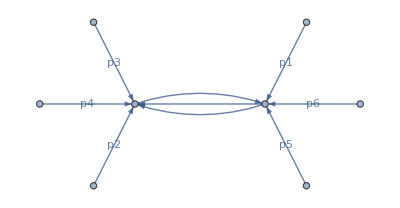

```mathematica
SubLaporta//Sort
```

```mathematica
Cases[PureIntegrals[[1]],_root,Infinity]//DeleteDuplicates
Cases[PureIntegrals[[2]],_root,Infinity]//DeleteDuplicates
Cases[PureIntegrals[[11]],_root,Infinity]//DeleteDuplicates
Position[PureIntegrals,root[-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2]][[All,1]]//DeleteDuplicates
```

{root[-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2]}

{root[-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2]}

{}

{1,2,6,9,16,18,20,22}

```mathematica
vectors={p[1],p[2],p[3],p[4]}
Delta5=Table[Expand[vectors[[i]]vectors[[j]]],{i,1,4},{j,1,4}];
Det[Expand[Delta5/.p4conv]/.mandelstamScalarProducts]
Delta5/.mandelstamScalarProducts//MatrixForm
```

{p[1],p[2],p[3],p[4]}

(s12^2 s23^2)/16-1/8 s12^2 s23 s234+1/8 s12 s123 s23 s234+(s12^2 s234^2)/16-1/8 s12 s123 s234^2+(s123^2 s234^2)/16+1/8 s12 s123 s23 s34-1/8 s12 s23^2 s34+1/8 s12 s123 s234 s34-1/8 s123^2 s234 s34+1/8 s12 s23 s234 s34+1/8 s123 s23 s234 s34+(s123^2 s34^2)/16-1/8 s123 s23 s34^2+(s23^2 s34^2)/16-1/8 s12 s23^2 s56+1/8 s12 s23 s234 s56-1/8 s123 s23 s234 s56-1/4 s12 s23 s34 s56+1/8 s123 s23 s34 s56-1/8 s23^2 s34 s56+(s23^2 s56^2)/16

(0 | s12/2 | 1/2 (-s12+s123-s23) | 1/2 (-s123+s23-s234+s56)
s12/2 | 0 | s23/2 | 1/2 (-s23+s234-s34)
1/2 (-s12+s123-s23) | s23/2 | 0 | s34/2
1/2 (-s123+s23-s234+s56) | 1/2 (-s23+s234-s34) | s34/2 | 0)

1/16 (s12^2 (s23-s234)^2+(s123 (s234-s34)+s23 (s34-s56))^2+2 s12 (s123 (s23-s234) s234+s123 (s23+s234) s34+s23 (-2 s34 s56-s23 (s34+s56)+s234 (s34+s56))))

```mathematica
Expand[-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2]
16 *Det[Delta5/.mandelstamScalarProducts]//Expand
```

s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2

s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2